## Set up the metric, compute the Einstein tensor etc.

```mathematica
NotebookDirectory[]
```

/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo

### Metric and reference metric

```mathematica
co = {r,t,x1,x2,x3};
Ndim = Length[co];
```

```mathematica
g=({{0, 1, 0, 0, 0}, {1, -Afun[r,t], 0, 0, 0}, {0, 0, Sfun[r,t]^2, 0, 0}, {0, 0, 0, Sfun[r,t]^2, 0}, {0, 0, 0, 0, Sfun[r,t]^2}});
gup=Inverse[g]//Simplify;
```

### Christoffel Symbols

```mathematica
Chr=Table[
Simplify[(1/2)*Sum[gup[[μ,α]]*(
D[g[[ν,α]],co[[ρ]]]+D[g[[ρ,α]],co[[ν]]]-D[g[[ν,ρ]],co[[α]]]),
{α,1,Ndim}]],
{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim}];
```

### Riemann tensor

```mathematica
Clear[λ]
```

```mathematica
Rdownfun[μ_,ν_,ρ_,σ_]:=Simplify[Sum[g[[μ,λ]](D[Chr[[λ,σ,ν]],co[[ρ]]] - D[Chr[[λ,ρ,ν]],co[[σ]]] + Sum[Chr[[λ,ρ,α]]*Chr[[α,σ,ν]],{α,1,Ndim}]-Sum[Chr[[λ,σ,α]]*Chr[[α,ρ,ν]],{α,1,Ndim}]),{λ,1,Ndim}]];
```

```mathematica
Rdown=Table[Rdownfun[μ,ν,ρ,σ],{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim},{σ,1,Ndim}];
```

```mathematica
Riemann=Table[Sum[gup[[μ,λ]]Rdown[[λ,ν,ρ,σ]],{λ,1,Ndim}],{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim},{σ,1,Ndim}];
```

### Ricci and Einstein tensors

```mathematica
Ricci=Table[Simplify[Sum[Riemann[[λ,μ,λ,ν]],{λ,1,Ndim}]],{μ,1,Ndim},{ν,1,Ndim}];
R=Sum[gup[[μ,ν]]Ricci[[μ,ν]],{μ,1,Ndim},{ν,1,Ndim}]//Simplify;
Einstein=Ricci-(1/2)R g//Simplify;
```

### Energy-momentum tensor

```mathematica
T=2Simplify[Table[D[Φfun[r,t],co[[μ]]]D[Φfun[r,t],co[[ν]]]-Vfun[Φfun[r,t]]g[[μ,ν]]-1/2 g[[μ]][[ν]]Sum[gup[[α]][[β]]D[Φfun[r,t],co[[α]]]D[Φfun[r,t],co[[β]]],{α,1,Ndim},{β,1,Ndim}],
{μ,1,Ndim},{ν,1,Ndim}]];
divPhi=Simplify[Sum[gup[[μ,ν]]D[D[Φfun[r,t],co[[μ]]],co[[ν]]],{μ,1,Ndim},{ν,1,Ndim}]-Sum[gup[[μ,ν]]Chr[[ρ,μ,ν]]D[Φfun[r,t],co[[ρ]]],{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim}]]
```

Afun^(1,0)[r,t] Φfun^(1,0)[r,t]+(3 (Φfun^(0,1)[r,t] Sfun^(1,0)[r,t]+(Sfun^(0,1)[r,t]+Afun[r,t] Sfun^(1,0)[r,t]) Φfun^(1,0)[r,t]))/Sfun[r,t]+2 Φfun^(1,1)[r,t]+Afun[r,t] Φfun^(2,0)[r,t]

## Equations of motion

```mathematica
Clear[Afun,Sfun,Φfun,Vfun]
```

```mathematica
Eqs=Simplify[gup.(Einstein-T)];
```

```mathematica
eq1=Simplify[Eqs[[2,1]]]
```

-2 (Φfun^(1,0)[r,t])^2-(3 Sfun^(2,0)[r,t])/Sfun[r,t]

```mathematica
soleq1=Solve[0==eq1,Derivative[2,0][Sfun][r,t]][[1]]
```

{Sfun^(2,0)[r,t]→-2/3 Sfun[r,t] (Φfun^(1,0)[r,t])^2}

```mathematica
eq2=Simplify[Eqs[[2,2]]//.soleq1]
```

2 Vfun[Φfun[r,t]]+(3 Sfun^(1,0)[r,t] (2 Sfun^(0,1)[r,t]+Afun[r,t] Sfun^(1,0)[r,t]))/Sfun[r,t]^2-Afun[r,t] (Φfun^(1,0)[r,t])^2+(3 (Afun^(1,0)[r,t] Sfun^(1,0)[r,t]+2 Sfun^(1,1)[r,t]))/(2 Sfun[r,t])

```mathematica
eq3=divPhi-Vfun'[Φfun[r,t]];
```

```mathematica
eq4=Eqs[[3,3]]//Simplify
```

2 Vfun[Φfun[r,t]]+(Sfun^(1,0)[r,t] (2 Sfun^(0,1)[r,t]+Afun[r,t] Sfun^(1,0)[r,t]))/Sfun[r,t]^2+2 Φfun^(0,1)[r,t] Φfun^(1,0)[r,t]+Afun[r,t] (Φfun^(1,0)[r,t])^2+1/2 Afun^(2,0)[r,t]+(2 (Afun^(1,0)[r,t] Sfun^(1,0)[r,t]+2 Sfun^(1,1)[r,t]+Afun[r,t] Sfun^(2,0)[r,t]))/Sfun[r,t]

```mathematica
eq5=2 Sfun[r,t]Eqs[[1,2]]//Simplify
```

-4 Sfun[r,t] Φfun^(0,1)[r,t] (Φfun^(0,1)[r,t]+Afun[r,t] Φfun^(1,0)[r,t])-3 (2 Sfun^(0,2)[r,t]-Sfun^(0,1)[r,t] Afun^(1,0)[r,t]+Afun^(0,1)[r,t] Sfun^(1,0)[r,t]+2 Afun[r,t] Sfun^(1,1)[r,t])

```mathematica
sys={eq1,eq2,eq3,eq4,eq5};
```

## Expansion near the boundary: Eddington-Finkelstein

```mathematica
ASPfilename="ASPsol.txt";
```

```mathematica
(*ASPsol=Get[ASPfilename];*)
sola4={Subscript[a, 4]'[t]->2/27 (36 M^2 ξ[t] ξ'[t]-18 M Subscript[p, 2]'[t]+(36 M^2 ξ[t]^2 S0'[t])/S0[t]+(9 M^2 S0'[t] S0''[t])/S0[t]^2+(2 ((4 M^4-27 Subscript[a, 4][t]-18 M Subscript[p, 2][t]) S0'[t]+6 M^2 Derivative[3][S0][t]))/S0[t])};
```

```mathematica
Clear[Afun,Sfun,Φfun,Vfun];
```

```mathematica
sysScaled={r^2 sys[[1]],sys[[2]],r sys[[3]],sys[[4]],1/r^2 sys[[5]]}//Simplify;
```

```mathematica
order=6;
```

```mathematica
Vfun[x_]:=1/2 (-x+x^3/4)^2-4/3 (-3/2-x^2/2+x^4/16)^2;
```

```mathematica
ASer[r_,t_,ord_]:=(r)^2 Sum[(Subscript[a, n][t]+Subscript[α1, n][t]Log[r]+Subscript[α2, n][t] Log[r]^2)(1/r)^n,{n,0,ord}];
```

```mathematica
SSer[r_,t_,ord_]:=(r)Sum[(Subscript[s, n][t]+Subscript[σ1, n][t]Log[r]+Subscript[σ2, n][t] Log[r]^2)(1/r)^n,{n,0,ord}];
```

```mathematica
PhiSer[r_,t_,ord_]:=(1/r)Sum[(Subscript[p, n][t]+Subscript[ψ1, n][t]Log[r]+Subscript[ψ2, n][t] Log[r]^2)(1/r)^n,{n,0,ord}];
```

```mathematica
BCs={Subscript[a, 0][t]->1,Subscript[a, 1][t]->2 ξ[t],Subscript[s, 0][t]->S0[t],Subscript[p, 0][t]->M};
```

```mathematica
LogToDel={Log[r]->δ};
```

```mathematica
sol=BCs;
Print["Total time: ",AbsoluteTiming[
Do[
Print["Order = ",ii,", time = ",AbsoluteTiming[
Afun[r_,t_]=ASer[r,t,ii]//.sol;
Sfun[r_,t_]=SSer[r,t,ii]//.sol;
Φfun[r_,t_]=PhiSer[r,t,ii]//.sol;

sysCoeff=SeriesCoefficient[sysScaled,{r,Infinity,ii}]//.LogToDel//Simplify;
EqHereL0=SeriesCoefficient[sysCoeff,{δ,0,0}];
EqHereL1=SeriesCoefficient[sysCoeff,{δ,0,1}];
EqHereL2=SeriesCoefficient[sysCoeff,{δ,0,2}];

EqHere=Join[EqHereL0,EqHereL1,EqHereL2];

VarsHere={Subscript[a, ii][t],Subscript[p, ii][t],Subscript[s, ii][t],Subscript[α1, ii][t],Subscript[α2, ii][t],Subscript[σ1, ii][t],Subscript[σ2, ii][t],Subscript[ψ1, ii][t],Subscript[ψ2, ii][t]};
DtVarsHere=D[VarsHere,t];

solHere=Solve[0==EqHere,Join[VarsHere,DtVarsHere]][[1]]//Quiet;
solHere2=DeleteCases[solHere,Derivative[_][_][_]->_];
sol=Join[sol,solHere2];

check=SeriesCoefficient[sysScaled,{r,Infinity,ii}]//.sol//.D[sol,t]//.sola4//Simplify;
][[1]],", equation check = ",check];
,{ii,0,order}]
][[1]]]
```

Order = 0, time = 0.669196, equation check = {0,0,0,0,0}

Order = 1, time = 0.659868, equation check = {0,0,0,0,0}

Order = 2, time = 0.807743, equation check = {0,0,0,0,0}

Order = 3, time = 1.40397, equation check = {0,0,0,0,0}

Order = 4, time = 2.30348, equation check = {0,0,0,0,0}

Order = 5, time = 6.08766, equation check = {0,0,0,0,0}

Order = 6, time = 19.6129, equation check = {0,0,0,0,0}

Total time: 31.5452

```mathematica
ASPsol=sol;
```

```mathematica
Put[ASPsol,ASPfilename];
```

## Expansion near the boundary: Fefferman-Graham

```mathematica
(*order=5;*)
```

In these coords, w =√ρ, the usual FG coordinate and z=r_EF^-1.

```mathematica
(*Clear[REF,TEF,G11,G22,A,CoEq,τ,r,ZEF,Afun]*)
```

```mathematica
(*FGco={w,t};
EFco={ZEF[w,t],TEF[w,t]};*)
```

```mathematica
(*ΛMat=Table[D[EFco[[μ]],FGco[[ν]]],{μ,1,2},{ν,1,2}];*)
```

```mathematica
(*FGmetric=DiagonalMatrix[{1/w^2,G11[w,t]}];*)
```

```mathematica
(*EFmetric={{0,-1/ZEF[w,t]^2},{-1/ZEF[w,t]^2,-Afun[1/ZEF[w,t],TEF[w,t]]}};*)
```

```mathematica
(*CoEq=Simplify[FGmetric-Transpose[ΛMat].EFmetric.ΛMat];*)
```

```mathematica
(*CoEq//MatrixForm*)
```

(1/w^2+Afun[1/ZEF[w,t],TEF[w,t]] (TEF^(1,0)[w,t])^2+(2 TEF^(1,0)[w,t] ZEF^(1,0)[w,t])/ZEF[w,t]^2 | (Afun[1/ZEF[w,t],TEF[w,t]] ZEF[w,t]^2 TEF^(0,1)[w,t] TEF^(1,0)[w,t]+ZEF^(0,1)[w,t] TEF^(1,0)[w,t]+TEF^(0,1)[w,t] ZEF^(1,0)[w,t])/ZEF[w,t]^2
(Afun[1/ZEF[w,t],TEF[w,t]] ZEF[w,t]^2 TEF^(0,1)[w,t] TEF^(1,0)[w,t]+ZEF^(0,1)[w,t] TEF^(1,0)[w,t]+TEF^(0,1)[w,t] ZEF^(1,0)[w,t])/ZEF[w,t]^2 | G11[w,t]+TEF^(0,1)[w,t] (Afun[1/ZEF[w,t],TEF[w,t]] TEF^(0,1)[w,t]+(2 ZEF^(0,1)[w,t])/ZEF[w,t]^2))

```mathematica
(*ZEFSer[w_,t_,ord_]:=Sum[(Subscript[Ρ, n][t]+Subscript[ρ1, n][t]Log[w](*+Subscript[ρ2, n][t] Log[w]^2*))w^n,{n,1,ord}];
TEFSer[w_,t_,ord_]:=t+Sum[(Subscript[Τ, n][t]+Subscript[τ1, n][t]Log[w](*+Subscript[τ2, n][t] Log[w]^2*))w^n,{n,1,ord}];*)
```

```mathematica
(*G11[w_,t_]:=-1/w^2+Sum[(Subscript[G0, n][t]+Subscript[G1, n][t]Log[w]+Subscript[G2, n][t] Log[w]^2)w^n,{n,0,order}];*)
```

```mathematica
(*CoordEq=w^3{CoEq[[1,1]],CoEq[[1,2]]};*)
```

```mathematica
(*sol={Subscript[τ1, 1][t]->0,Subscript[Τ, 1][t]->-1};
LogToDel={Log[w]->δ};
Print["Total time: ",AbsoluteTiming[
Do[
Print["Order = ",ii,", time = ",AbsoluteTiming[
Afun[r_,t_]=ASer[r,t,ii]//.ASPsol;
ZEF[w_,t_]=ZEFSer[w,t,ii]//.sol;
TEF[w_,t_]=TEFSer[w,t,ii]//.sol;

sysCoeff=SeriesCoefficient[CoordEq,{w,0,ii}]//.LogToDel//Simplify;
EqHereL0=SeriesCoefficient[sysCoeff,{δ,0,0}];
EqHereL1=SeriesCoefficient[sysCoeff,{δ,0,1}];
(*EqHereL2=SeriesCoefficient[sysCoeff,{δ,0,2}];*)

EqHere=Join[EqHereL0,EqHereL1(*,EqHereL2*)];

VarsHere={Subscript[Ρ, ii][t],Subscript[Τ, ii][t],Subscript[ρ1, ii][t](*,Subscript[ρ2, ii][t]*),Subscript[τ1, ii][t](*,Subscript[τ2, ii][t]*)};
DtVarsHere=D[VarsHere,t];

solHere=Solve[0==EqHere,Join[VarsHere,DtVarsHere]][[1]]//Quiet;
solHere2=DeleteCases[solHere,Derivative[_][_][_]->_];
sol=Join[sol,solHere2];

check=SeriesCoefficient[CoordEq,{w,0,ii}]//.sol//.D[sol,t]//.sola4//Simplify;
][[1]],", equation check = ",check];
,{ii,1,order}]
][[1]]]*)
```

Order = 1, time = 0.055222, equation check = {0,0}

Order = 2, time = 1.33436, equation check = {0,0}

Order = 3, time = 0.466835, equation check = {0,0}

Order = 4, time = 13.7499, equation check = {0,0}

Order = 5, time = 99.6919, equation check = {0,0}

Total time: 115.299

```mathematica
(*FGsol=sol;*)
```

```mathematica
(*GttExpr=-w^2(TEF^(0,1)[w,t] (Afun[1/ZEF[w,t],TEF[w,t]] TEF^(0,1)[w,t]+(2 ZEF^(0,1)[w,t])/ZEF[w,t]^2))//.FGsol;*)
```

```mathematica
(*Gtt0=SeriesCoefficient[GttExpr,{w,0,0}]//Simplify*)
```

-1

```mathematica
(*Gtt2=SeriesCoefficient[GttExpr,{w,0,2}]//Simplify*)
```

M^2/3-S_0'[t]^2/(2 S_0[t]^2)+S_0''[t]/S_0[t]

```mathematica
(*Gtt4=SeriesCoefficient[GttExpr,{w,0,4}]//.{Log[1/w]->0}//Simplify*)
```

$Aborted

```mathematica
(*Htt4=-1/2 Coefficient[SeriesCoefficient[GttExpr,{w,0,4}],Log[1/w]]//Simplify*)
```

(M^2 S_0''[t])/(4 S_0[t])

```mathematica
(*GxxExpr=w^2 SSer[1/ZEF[w,t],TEF[w,t],order]^2;*)
```

```mathematica
(*Gxx0=SeriesCoefficient[GxxExpr,{w,0,0}]//.Join[FGsol,ASPsol,D[ASPsol,t],D[ASPsol,{t,2}]]//Simplify*)
```

S_0[t]^2

```mathematica
(*Gxx2=SeriesCoefficient[GxxExpr,{w,0,2}]//.Join[FGsol,ASPsol,D[ASPsol,t],D[ASPsol,{t,2}]]//Simplify*)
```

1/6 (-2 M^2 S_0[t]^2-3 S_0'[t]^2)

```mathematica
(*Gxx4=SeriesCoefficient[GxxExpr,{w,0,4}]//.Join[{Log[1/w]->0},FGsol,ASPsol,D[ASPsol,t],D[ASPsol,{t,2}],D[ASPsol,{t,3}],D[ASPsol,{t,4}]]//Simplify*)
```

(4 (19 M^4+72 M^2 ξ[t]^2-27 a_4[t]-72 M p_2[t]) S_0[t]^4+27 S_0'[t]^4+204 M^2 S_0[t]^3 S_0''[t])/(432 S_0[t]^2)

```mathematica
(*Hxx4=-1/2Coefficient[SeriesCoefficient[GxxExpr,{w,0,4}]//.Join[FGsol,ASPsol,D[ASPsol,t],D[ASPsol,{t,2}],D[ASPsol,{t,2}],D[ASPsol,{t,3}],D[ASPsol,{t,4}]],Log[1/w]]//Simplify*)
```

-1/12 M^2 (2 S_0'[t]^2+S_0[t] S_0''[t])

## Evolution equations

```mathematica
Clear[Afun,Sfun,Φfun,Vfun]
```

```mathematica
D[f[r,t],{t,2}]
```

f^(0,2)[r,t]

```mathematica
replDDt={Derivative[0,2][f_][r,t]->Subscript[f, dd][r,t]-(1/2 Derivative[0,1][Afun][r,t]Derivative[1,0][f][r,t]+Afun[r,t]Derivative[1,1][f][r,t]+1/4 Afun[r,t]Derivative[1,0][Afun][r,t]Derivative[1,0][f][r,t]+1/4 Afun[r,t]^2 Derivative[2,0][f][r,t]) };
```

```mathematica
replDt={Derivative[0,1][f_][r,t]->Subscript[f, d][r,t]-1/2 Afun[r,t]Derivative[1,0][f][r,t]};
```

```mathematica
replDrDt=D[replDt,r]//Simplify;
```

```mathematica
sol1=Solve[0==eq1,Derivative[2,0][Sfun][r,t]][[1]]//Simplify
```

{Sfun^(2,0)[r,t]→-2/3 Sfun[r,t] (Φfun^(1,0)[r,t])^2}

```mathematica
tmp=sys[[2]]//.replDrDt//.replDt//.sol1//Simplify;
```

```mathematica
sol2=Solve[0==tmp,Derivative[1,0][Subscript[Sfun, d]][r,t]][[1]]//Simplify
```

{Sfun_d^(1,0)[r,t]→-2/3 Sfun[r,t] Vfun[Φfun[r,t]]-(2 Sfun_d[r,t] Sfun^(1,0)[r,t])/Sfun[r,t]}

```mathematica
tmp=sys[[3]]//.replDrDt//.replDt//Simplify;
```

```mathematica
sol3=Solve[0==tmp,Derivative[1,0][Subscript[Φfun, d]][r,t]][[1]]//Simplify//Expand
```

{Φfun_d^(1,0)[r,t]→1/2 Vfun'[Φfun[r,t]]-(3 Φfun_d[r,t] Sfun^(1,0)[r,t])/(2 Sfun[r,t])-(3 Sfun_d[r,t] Φfun^(1,0)[r,t])/(2 Sfun[r,t])}

```mathematica
tmp=sys[[4]]//.replDrDt//.replDt//.sol1//.sol2//Simplify;
```

```mathematica
sol4=Solve[0==tmp,Derivative[2,0][Afun][r,t]][[1]]//Simplify//Expand
```

{Afun^(2,0)[r,t]→4/3 Vfun[Φfun[r,t]]+(12 Sfun_d[r,t] Sfun^(1,0)[r,t])/Sfun[r,t]^2-4 Φfun_d[r,t] Φfun^(1,0)[r,t]}

```mathematica
tmp=sys[[5]]//.replDDt//.replDrDt//.replDt//.Join[sol1,sol2,sol3,sol4]//Simplify;
```

```mathematica
tmp
```

-6 Sfun_dd[r,t]-4 Sfun[r,t] Φfun_d[r,t]^2+3 Sfun_d[r,t] Afun^(1,0)[r,t]

```mathematica
sol5=Solve[0==tmp,Subscript[Sfun, dd][r,t]][[1]]//Simplify//Expand
```

{Sfun_dd[r,t]→-2/3 Sfun[r,t] Φfun_d[r,t]^2+1/2 Sfun_d[r,t] Afun^(1,0)[r,t]}

```mathematica
evolEqs={Derivative[2,0][Sfun][r,t]-(Derivative[2,0][Sfun][r,t]/.sol1),Derivative[1,0][Subscript[Sfun, d]][r,t]-(Derivative[1,0][Subscript[Sfun, d]][r,t]/.sol2),Derivative[1,0][Subscript[Φfun, d]][r,t]-(Derivative[1,0][Subscript[Φfun, d]][r,t]/.sol3),Derivative[2,0][Afun][r,t]-(Derivative[2,0][Afun][r,t]/.sol4)};
```

```mathematica
constrEq=Subscript[Sfun, dd][r,t]-(Subscript[Sfun, dd][r,t]/.sol5);
```

## ‘Subtracted’ variables

```mathematica
order=6;
```

```mathematica
Clear[Sdot,Sfun,Phidot,Φfun,Afun,ii,S0];
```

```mathematica
SdotSer[r_,t_,ord_]:=(r)^2 Sum[(Subscript[sd, n][t]+Subscript[σd1, n][t]Log[r]+Subscript[σd2, n][t] Log[r]^2)(1/r)^n,{n,0,ord}];
```

```mathematica
PhidotSer[r_,t_,ord_]:=Sum[(Subscript[pd, n][t]+Subscript[ψd1, n][t]Log[r]+Subscript[ψd2, n][t] Log[r]^2)(1/r)^n,{n,0,ord}];
```

```mathematica
dotdef={1/r^2(Sdot[r,t]-(D[Sfun[r,t],t]+1/2 Afun[r,t]D[Sfun[r,t],r])),Phidot[r,t]-(D[Φfun[r,t],t]+1/2 Afun[r,t]D[Φfun[r,t],r])};
```

```mathematica
sol={Subscript[ψd1, 0][t]->0};
LogToDel={Log[r]->δ};
Print["Total time: ",AbsoluteTiming[
Do[
Print["Order = ",ii,", time = ",AbsoluteTiming[
Sdot[r_,t_]=SdotSer[r,t,ii]//.sol;
Phidot[r_,t_]=PhidotSer[r,t,ii]//.sol;

Afun[r_,t_]=ASer[r,t,ii]//.ASPsol;
Sfun[r_,t_]=SSer[r,t,ii]//.ASPsol;
Φfun[r_,t_]=PhiSer[r,t,ii]//.ASPsol;

sysCoeff=SeriesCoefficient[dotdef,{r,Infinity,ii}]//.LogToDel//Simplify;
EqHereL0=SeriesCoefficient[sysCoeff,{δ,0,0}];
EqHereL1=SeriesCoefficient[sysCoeff,{δ,0,1}];
EqHereL2=SeriesCoefficient[sysCoeff,{δ,0,2}];

EqHere=Join[EqHereL0,EqHereL1,EqHereL2];

VarsHere={Subscript[sd, ii][t],Subscript[pd, ii][t],Subscript[σd1, ii][t],Subscript[σd2, ii][t],Subscript[ψd1, ii][t],Subscript[ψd2, ii][t]};
DtVarsHere=D[VarsHere,t];

solHere=Solve[0==EqHere,Join[VarsHere,DtVarsHere]][[1]]//Quiet;
solHere2=DeleteCases[solHere,Derivative[_][_][_]->_];
sol=Join[sol,solHere2];

check=SeriesCoefficient[dotdef,{r,Infinity,ii}]//.sol//.D[sol,t]//.sola4//Simplify;
][[1]],", equation check = ",check];
,{ii,0,order}]
][[1]]]
```

Order = 0, time = 0.017011, equation check = {0,0}

Order = 1, time = 0.019946, equation check = {0,0}

Order = 2, time = 0.105926, equation check = {0,0}

Order = 3, time = 0.175788, equation check = {0,0}

Order = 4, time = 0.397647, equation check = {0,0}

Order = 5, time = 0.808739, equation check = {0,0}

Order = 6, time = 2.41821, equation check = {0,0}

Total time: 3.94368

```mathematica
PSDotSol=sol;
```

```mathematica
Clear[Sdot,Sfun,Phidot,Φfun,Afun,Vfun,ii];
```

```mathematica
replWithSub={
Afun[r,t]->((r^2 Subscript[a, 0][t]+r Subscript[a, 1][t]+Subscript[a, 2][t]+(Log[r] Subscript[α1, 4][t])/r^2+(Log[r] Subscript[α1, 5][t])/r^3)/.ASPsol)+ASub[r,t]/r^2,
Sfun[r,t]->(((r Subscript[s, 0][t]+Subscript[s, 1][t]+(Subscript[s, 2][t])/r+(Subscript[s, 3][t])/r^2)+((Log[r] Subscript[σ1, 4][t])/r^3+(Log[r] Subscript[σ1, 5][t])/r^4+(Log[r] Subscript[σ1, 6][t])/r^5)+(Log[r]^2 Subscript[σ2, 6][t])/r^5)//.ASPsol)+SSub[r,t]/r^3,
Φfun[r,t]->((((Subscript[p, 0][t])/r+(Subscript[p, 1][t])/r^2)+((Log[r] Subscript[ψ1, 2][t])/r^3+(Log[r] Subscript[ψ1, 3][t])/r^4))/.ASPsol)+PhiSub[r,t]/r^3,
Subscript[Sfun, d][r,t]->(((r^2 Subscript[sd, 0][t]+r Subscript[sd, 1][t]+Subscript[sd, 2][t]+(Subscript[sd, 3][t])/r)+((Log[r] Subscript[σd1, 4][t])/r^2+(Log[r] Subscript[σd1, 5][t])/r^3(*+(Log[r] Subscript[σd1, 6][t])/r^4*)))/.PSDotSol)+SdotSub[r,t]/r^2,
Subscript[Φfun, d][r,t]->((Subscript[pd, 0][t]+((Log[r] Subscript[ψd1, 2][t])/r^2+(Log[r] Subscript[ψd1, 3][t])/r^3))/.PSDotSol)+PhidotSub[r,t]/r^2

};
```

```mathematica
Clear[S0]
```

```mathematica
Clear[Sdot,Sfun,Phidot,Φfun,Afun,ii];
```

```mathematica
replWithSub=Join[replWithSub,D[replWithSub,r],D[replWithSub,{r,2}]]//Simplify;
```

```mathematica
ScaledEvolEqs={r^3 evolEqs[[1]],r^2 evolEqs[[2]],r^2 evolEqs[[3]],evolEqs[[4]]}//.replWithSub;
```

```mathematica
SeriesCoefficient[PhiSer[r,t,2],{r,Infinity,3}]//.ASPsol//Expand//Simplify
```

p_2[t]-(M Log[r] (S0'[t]^2+S0[t] S0''[t]))/(2 S0[t]^2)

#### Boundary conditions

```mathematica
tmp=r^2(SdotSer[r,t,5]-(((r^2 Subscript[sd, 0][t]+r Subscript[sd, 1][t]+Subscript[sd, 2][t]+(Subscript[sd, 3][t])/r)+((Log[r] Subscript[σd1, 4][t])/r^2+(Log[r] Subscript[σd1, 5][t])/r^3))))//.PSDotSol//Simplify;
```

```mathematica
sdotbdry=SeriesCoefficient[tmp,{r,Infinity,0}]//Simplify//Expand
```

-5/36 M^4 S0[t]-1/2 M^2 S0[t] ξ[t]^2+1/2 S0[t] a_4[t]+1/2 M S0[t] p_2[t]+2/9 M^2 ξ[t] S0'[t]+(3 M^2 S0'[t]^2)/(16 S0[t])-61/144 M^2 S0''[t]

```mathematica
tmp=r^2(ASer[r,t,4]-((r^2 Subscript[a, 0][t]+r Subscript[a, 1][t]+Subscript[a, 2][t]+(Log[r] Subscript[α1, 4][t])/r^2+(Log[r] Subscript[α1, 5][t])/r^3)))//.ASPsol//Simplify;
```

```mathematica
Series[tmp,{r,Infinity,0}]
```

a_4[t]+O[1/r]^1

## Routines for writing out

```mathematica
ClearAll[ToJuliaForm,variables,fields,coeffLabels,makeJuliaFunc,str];
```

```mathematica
(*---1. Julia-compatible symbolic conversion---*)
ToJuliaForm[expr_]:=Module[{s},s=ToString[expr//InputForm];
s=StringReplace[s,{"Sin["->"sin(","Sinh["->"sinh(","Cos["->"cos(","Cosh["->"cosh(","Tan["->"tan(","Tanh["->"tanh(","Sech["->"sech(","Exp["->"exp(","Log["->"log(","Sqrt["->"sqrt(","Vfun["->"Vfun(","Derivative[1][Vfun]["->"DV(","]"->")"}];
s];
```

```mathematica
(*---2. Variable names to unpack from struct---*)
variables={"Phi","S","Sdot","Phidot","A","PhiZ","SZ","SdotZ","PhidotZ","AZ","PhiZZ","SZZ","SdotZZ","PhidotZZ","AZZ","z","LN","t","X","p2","a4","DS0","DS1","DS2","DS3","DS4"};

(*---3. Field names and coefficient labels---*)
fields={"Phi","S","Sdot","Phidot","A"};
coeffLabels={"Coeff0","Coeff1","Coeff2","Src"};
```

```mathematica
(*---4. Build a single Julia function as text---*)
makeJuliaFunc[field_,label_,expr_]:=Module[{fname},fname=field<>label;
"function "<>fname<>"(v::PDEVars{T}) where {T}\n\n"<>"    @unpack "<>StringRiffle[variables,", "]<>" = v\n\n"<>"    co = "<>ToString[InputForm[expr]]<>"\n\n
"<>"    return co\nend\n\n"];

makeJuliaFuncBdry[field_,label_,expr_,exprB_]:=Module[{fname},fname=field<>label;
"function "<>fname<>"(v::PDEVars{T}) where {T}\n\n"<>"    @unpack "<>StringRiffle[variables,", "]<>" = v\n\n"<>"if z == 0 \n co = "<>ToJuliaForm[ToString[InputForm[exprB]]]
<>";\n else \n    co = "<>ToJuliaForm[ToString[InputForm[expr]]]<>";\nend\n\n
"<>"    return co\nend\n\n"];
```

```mathematica
JuliaFuncStart[field_,label_]:=Module[{fname},fname=field<>label;"function "<>fname<>"(v::PDEVars{T}) where {T}\n\n"<>"    @unpack "<>StringRiffle[variables,", "]<>" = v\n\n"];
```

```mathematica
(*---5. Begin file string---*)
strStart="
# ==============================================
#  Auto-generated Julia code from Mathematica
#  Do not edit manually
# ==============================================


# ----------------------------------------------
#  Generated functions
# ----------------------------------------------

";
```

### Write out conversions between variables

```mathematica
(*Vars={PhiSub[z],SSub[z],SdotSub[z],PhidotSub[z],ASub[z]};
varnames={"Phi","S","Sdot","Phidot","A"};*)
```

```mathematica
(*replfun=Table[{Vars[[ii]]->ToExpression[varnames[[ii]]],D[Vars[[ii]],z]->ToExpression[varnames[[ii]]<>"Z"],D[Vars[[ii]],{z,2}]->ToExpression[varnames[[ii]]<>"ZZ"]},{ii,1,Length[Vars]}]//Flatten;
replfun=Join[replfun,{ξ[t]->X,Vfun'[x_]->DV[x],Subscript[p, 2][t]->p2,Subscript[a, 4][t]->a4,Log[1/z]->LN}];*)
```

```mathematica
(*RtoZ={f_^(2,0)[r,t]->z^4 f^(2,0)[z,t]+2 z^3 f^(1,0)[z,t],f_^(1,0)[r,t]->-z^2f^(1,0)[z,t],f_[r,t]->f[z,t],r->1/z};*)
```

```mathematica
(*replDS0=Table[D[S0[t],{t,ii}]->ToExpression["DS"<>ToString[ii]],{ii,0,6}];*)
```

```mathematica
(*funs={Φfun,Sfun,Subscript[Sfun, d],Subscript[Φfun, d],Afun};*)
```

```mathematica
(*subfuns={PhiSub,SSub,SdotSub,PhidotSub,ASub};*)
```

```mathematica
(*tmprepl=replWithSub[[1;;5]]//.RtoZ//Simplify;*)
```

```mathematica
(*tmpinvrepl=Solve[0==Table[funs[[ii]][z,t]-(funs[[ii]][z,t]//.tmprepl),{ii,1,5}],Table[subfuns[[ii]][z,t],{ii,1,5}]][[1]]//Simplify;*)
```

```mathematica
(*str=strStart;
Do[str=str<>"function "<>fields[[ii]]<>"_to_unsub(params, z, sub_value)\n\n"<>"t, X, p2, a4 = params;\n"<>fields[[ii]]<>" = sub_value;\n";
str=str<>"unsub_value = "<>ToString[InputForm[funs[[ii]][z,t]//.tmprepl//.replfun//.replDS0//.{ξ'[t]->XPrime}]]<>";\n\n";
str=str<>"end\n\n";
,{ii,1,5}]*)
```

```mathematica
(*str*)
```

## Final equations

### Compute

```mathematica
Clear[SSub,PhiSub,S0,ξ,M,Vfun,SdotSub]
```

```mathematica
RtoZ={Derivative[2,0][f_][r,t]->z^4 Derivative[2,0][f][z,t]+2 z^3 Derivative[1,0][f][z,t],Derivative[1,0][f_][r,t]->-z^2 Derivative[1,0][f][z,t],f_[r,t]->f[z,t],r->1/z};
```

```mathematica
replDS0=Table[D[S0[t],{t,ii}]->ToExpression["DS"<>ToString[ii]],{ii,0,6}];
```

```mathematica
toODE={Derivative[2,0][f_][z,t]->f''[z],Derivative[1,0][f_][z,t]->f'[z],f_[z,t]->f[z]};
```

```mathematica
tmpeq=evolEqs[[1]]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
SEq=z^-5 tmpeq//.toODE//Simplify;
```

```mathematica
SCoeffs=Reverse[{Coefficient[SEq,SSub''[z]],Coefficient[SEq,SSub'[z]],Coefficient[SEq,SSub[z]],SEq//.{SSub[z]->0,SSub'[z]->0,SSub''[z]->0}}]//Simplify;
```

```mathematica
Simplify[SEq-SCoeffs.{1,SSub[z],SSub'[z],SSub''[z]}]
```

0

```mathematica
SCoeffsB=SeriesCoefficient[SCoeffs,{z,0,0}]//.{PhiSub[0]->Subscript[p, 2][t]}//Simplify;
```

```mathematica
SCoeffsB
```

{-(M (4 S0[t]^2 (M^3-18 p_2[t])+9 M S0'[t]^2+S0[t] (48 M ξ[t] S0'[t]+9 M S0''[t])))/(18 S0[t]),12,0,0}

```mathematica
tmpeq=evolEqs[[2]]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
SdotEq=-z^-4 tmpeq//.toODE//Simplify;
```

```mathematica
SdotCoeffs=Reverse[{Coefficient[SdotEq,SdotSub''[z]],Coefficient[SdotEq,SdotSub'[z]],Coefficient[SdotEq,SdotSub[z]],SdotEq//.{SdotSub[z]->0,SdotSub'[z]->0}}]//Simplify;
```

```mathematica
Simplify[SdotEq-SdotCoeffs.{1,SdotSub[z],SdotSub'[z],SdotSub''[z]}]
```

0

```mathematica
SCoeffs[[1]]//.{S0->(1&),ξ[t]->0,PhiSub[z]->0,PhiSub'[z]->0}//Simplify
```

-(2 M^4)/9

```mathematica
2/9//N
```

0.222222

```mathematica
Vfun[x_]:=1/2 (-x+x^3/4)^2-4/3 (-3/2-x^2/2+x^4/16)^2;
```

```mathematica
(*Series[SdotCoeffs,{z,0,0}]//.{PhiSub[0]->Subscript[p, 2][t],SSub[0]->-SCoeffsB[[1]]/SCoeffsB[[2]],S0->(1&),M->1}//Simplify*)
```

$Aborted

```mathematica
SdotCoeffsB = {-sdotbdry,1,0,0};
```

```mathematica
Clear[Vfun];
```

```mathematica
tmpeq=evolEqs[[3]]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
PhidotEq=-z^-3 tmpeq//.toODE//Simplify;
```

```mathematica
PhidotCoeffs=Reverse[{Coefficient[PhidotEq,PhidotSub''[z]],Coefficient[PhidotEq,PhidotSub'[z]],Coefficient[PhidotEq,PhidotSub[z]],PhidotEq//.{PhidotSub[z]->0,PhidotSub'[z]->0}}]//Simplify;
```

```mathematica
Simplify[PhidotEq-PhidotCoeffs.{1,PhidotSub[z],PhidotSub'[z],PhidotSub''[z]}]
```

0

```mathematica
SdotCoeffs[[3]]
```

1

```mathematica
Vfun[x_]:=1/2 (-x+x^3/4)^2-4/3 (-3/2-x^2/2+x^4/16)^2;
```

```mathematica
PhidotCoeffsB=SeriesCoefficient[PhidotCoeffs,{z,0,0}]//.{PhiSub[0]->Subscript[p, 2][t]}//Simplify
```

{(-2 S0[t]^2 (2 M^3+9 M ξ[t]^2-9 p_2[t])+9 M S0'[t]^2-9 M S0[t] S0''[t])/(24 S0[t]^2),1/2,0,0}

```mathematica
Clear[Vfun];
```

```mathematica
tmpeq=evolEqs[[4]]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
AEq=z^-4 tmpeq//.toODE//Simplify;
```

```mathematica
ACoeffs=Reverse[{Coefficient[AEq,ASub''[z]],Coefficient[AEq,ASub'[z]],Coefficient[AEq,ASub[z]],AEq//.{ASub[z]->0,ASub'[z]->0,ASub''[z]->0}}]//Simplify;
```

```mathematica
Simplify[AEq-ACoeffs.{1,ASub[z],ASub'[z],ASub''[z]}]
```

0

```mathematica
Vfun[x_]:=1/2 (-x+x^3/4)^2-4/3 (-3/2-x^2/2+x^4/16)^2;
```

```mathematica
ACoeffsB={-Subscript[a, 4][t],1,0,0};
(*SeriesCoefficient[ACoeffs,{z,0,4}]//.{PhidotSub[0]->-PhidotCoeffsB[[1]]/PhidotCoeffsB[[2]],SdotSub[0]->sdotbdry,PhiSub[0]->Subscript[p, 2][t],SSub[0]->-SCoeffsB[[1]]/SCoeffsB[[2]]}//Simplify*)
```

```mathematica
Clear[Vfun];
```

```mathematica
finaleqs={SEq,SdotEq,PhidotEq,AEq};
```

```mathematica
{Coefficient[SEq,SSub''[z]],Coefficient[SdotEq,SdotSub'[z]],Coefficient[PhidotEq,PhidotSub'[z]],Coefficient[AEq,ASub''[z]]}//Simplify
```

{z^2,1,z,z^2}

```mathematica
Vars={PhiSub[z],SSub[z],SdotSub[z],PhidotSub[z],ASub[z]};
varnames={"Phi","S","Sdot","Phidot","A"};
```

```mathematica
replfun=Table[{Vars[[ii]]->ToExpression[varnames[[ii]]],D[Vars[[ii]],z]->ToExpression[varnames[[ii]]<>"Z"],D[Vars[[ii]],{z,2}]->ToExpression[varnames[[ii]]<>"ZZ"]},{ii,1,Length[Vars]}]//Flatten;
replfun=Join[replfun,{ξ[t]->X,Subscript[p, 2][t]->p2,Subscript[a, 4][t]->a4,Log[1/z]->LN}];
```

```mathematica
Vfun[z]//.replfun//InputForm//ToString
```

Vfun[z]

```mathematica
Clear[S0]
```

```mathematica
Sform[t_]:=Exp[(H t)/2](Cosh[Om (t-tstar)]/Cosh[Om*tstar])^(H/(2Om));
```

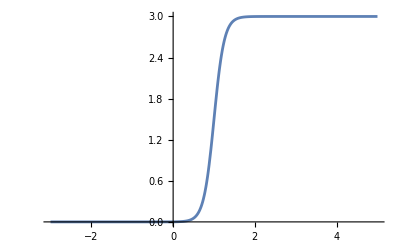

```mathematica
Plot[Sform'[t]/Sform[t]//.{H->3,Om->4,tstar->1},{t,-3,5}]
```

### Write out coefficients

```mathematica
(*---2. Variable names to unpack from struct---*)
variables={"Phi","S","Sdot","Phidot","A","PhiZ","SZ","SdotZ","PhidotZ","AZ","PhiZZ","SZZ","SdotZZ","PhidotZZ","AZZ","z","LN","t","X","p2","a4","DS0","DS1","DS2","DS3","DS4"};

(*---3. Field names and coefficient labels---*)
fields={"Phi","S","Sdot","Phidot","A"};
coeffLabels={"Coeff0","Coeff1","Coeff2","Src"};
```

```mathematica
makeJuliaFuncBdry[field_,label_,expr_,exprB_]:=Module[{fname},fname=field<>label;
"function "<>fname<>"(v::PDEVars{T}) where {T}\n\n"<>"    @unpack "<>StringRiffle[variables,", "]<>" = v\n\n"<>"if z == 0 \n co = "<>ToJuliaForm[ToString[InputForm[exprB]]]
<>";\n else \n    co = "<>ToJuliaForm[ToString[InputForm[expr]]]<>";\nend\n\n
"<>"    return co\nend\n\n"];
```

```mathematica
(*---1. Julia-compatible symbolic conversion---*)
ToJuliaForm[expr_]:=Module[{s},s=ToString[expr//FortranForm];
s=StringReplace[s,{"Sin["->"sin(","Sinh["->"sinh(","Cos["->"cos(","Cosh["->"cosh(","Tan["->"tan(","Tanh["->"tanh(","Sech["->"sech(","Exp["->"exp(","Log["->"log(","Sqrt["->"sqrt(","Vfun["->"Vfun(","Derivative[1][Vfun]["->"DV(","]"->")","\""->"","**"->"^"}];
s];
```

```mathematica
cosmocoeffs={SCoeffs,SdotCoeffs,PhidotCoeffs,ACoeffs};
cosmocoeffsB={SCoeffsB,SdotCoeffsB,PhidotCoeffsB,ACoeffsB};
```

```mathematica
str=strStart;

For[var=1,var<=4,var++,
field=fields[[var+1]];
For[ii=1,ii<4,ii++,
label=coeffLabels[[ii]];
str=str<>makeJuliaFuncBdry[field,label,(cosmocoeffs[[var,ii+1]]//.replfun//.replDS0),cosmocoeffsB[[var,ii+1]]//.replfun//.replDS0];
];
label=coeffLabels[[4]];
str=str<>makeJuliaFuncBdry[field,label,(cosmocoeffs[[var,1]]//.replfun//.replDS0),cosmocoeffsB[[var,1]]//.replfun//.replDS0];
];
```

```mathematica
str=StringReplace[str,".*" ->"."<>" "<>"*"];
```

```mathematica
strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/Equation expressions/ODECoeffExpr.jl"];
WriteString[strfile,str];
Close[strfile];
```

```mathematica
cosmocoeffs[[1,1]]//.{PhiSub'[z]->0}
```

1/(32400 z^2 S0[t]^9)((2 S0[t]^3 (M+3 z^2 PhiSub[z]-2 M z ξ[t])+2 M z^3 (-1+4 Log[1/z]) S0'[t]^3+M z^2 S0[t] S0'[t] ((1-3 Log[1/z]+3 z (-1+4 Log[1/z]) ξ[t]) S0'[t]+z (1-4 Log[1/z]) S0''[t])+M z^2 S0[t]^2 ((1-3 Log[1/z]+3 z (-1+4 Log[1/z]) ξ[t]) S0''[t]+z (1-4 Log[1/z]) S0^(3)[t]))^2 (1800 S0[t]^4 (3-M^2 z^2+z (3+M^2 z^2) ξ[t])+3 M^2 z^6 (199-90 Log[1/z]) Log[1/z] S0'[t]^4-9 M^2 z^5 Log[1/z] S0[t] S0'[t]^2 (-100 (-1+4 z ξ[t]) S0'[t]+3 z (53+20 Log[1/z]) S0''[t])+M z^4 Log[1/z] S0[t]^2 (20 (45 M+23 M^3 z^2-135 M z ξ[t]+216 M z^2 ξ[t]^2+54 z^2 p_2[t]) S0'[t]^2+6 M z^2 (247-45 Log[1/z]) S0''[t]^2-15 M z S0'[t] (84 (-1+4 z ξ[t]) S0''[t]-47 z S0^(3)[t]))+5 S0[t]^3 (-120 z (-9+M^2 z^2) S0'[t]+M z^4 Log[1/z] (4 (45 M+28 M^3 z^2-135 M z ξ[t]+216 M z^2 ξ[t]^2+54 z^2 p_2[t]) S0''[t]+3 M z (-48 (-1+4 z ξ[t]) S0^(3)[t]+25 z S0^(4)[t]))))+6 M S0[t]^6 (3600 M S0[t]^4 (-1+3 z ξ[t])-3 M z^4 (2369-7950 Log[1/z]+2700 Log[1/z]^2) S0'[t]^4+9 M z^3 S0[t] S0'[t]^2 (100 (9-20 Log[1/z]+4 z (-11+30 Log[1/z]) ξ[t]) S0'[t]-3 z (-543+1150 Log[1/z]+600 Log[1/z]^2) S0''[t])+z^2 S0[t]^2 (20 (M (-315-253 M^2 z^2+30 (18+23 M^2 z^2) Log[1/z])-135 M z (-9+20 Log[1/z]) ξ[t]+216 M z^2 (-11+30 Log[1/z]) ξ[t]^2+54 z^2 (-11+30 Log[1/z]) p_2[t]) S0'[t]^2-6 M z^2 (2807-8400 Log[1/z]+1350 Log[1/z]^2) S0''[t]^2-15 M z S0'[t] (84 (9-20 Log[1/z]+4 z (-11+30 Log[1/z]) ξ[t]) S0''[t]+47 z (11-30 Log[1/z]) S0^(3)[t]))+5 z S0[t]^3 (-720 M S0'[t]+z (4 (-7 M (45+44 M^2 z^2)+60 M (9+14 M^2 z^2) Log[1/z]-135 M z (-9+20 Log[1/z]) ξ[t]+216 M z^2 (-11+30 Log[1/z]) ξ[t]^2+54 z^2 (-11+30 Log[1/z]) p_2[t]) S0''[t]+3 M z (-48 (9-20 Log[1/z]+4 z (-11+30 Log[1/z]) ξ[t]) S0^(3)[t]+25 z (-11+30 Log[1/z]) S0^(4)[t])))))

```mathematica
str
```

```mathematica
str=strStart;
For[ii = 0, ii<=6,ii++,
str=str<>"function DS"<>ToString[ii]<>"f(t)\n\n";
str=str<>"res = "<>ToString[Simplify[D[Sform[t],{t,ii}]]//ToJuliaForm]<>"; \n\n";
str=str<>"return res;\nend\n\n";
];
```

```mathematica
str=StringReplace[str,".*" ->"."<>" "<>"*"];
```

```mathematica
(*strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/Equation expressions/CosmoS0Expr.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

```mathematica
str
```

# ==============================================
#  Auto-generated Julia code from Mathematica
#  Do not edit manually
# ==============================================


# ----------------------------------------------
#  Generated functions
# ----------------------------------------------

function DS0f(t)

res = E^((H*t)/2.)*(Cosh(Om*(t - tstar))*Sech(Om*tstar))^(H/(2. *Om)); 

return res;
end

function DS1f(t)

res = (E^((H*t)/2.)*H*(Cosh(Om*(t - tstar))*Sech(Om*tstar))^(H/(2. *Om))*(1 + Tanh(Om*(t - tstar))))/2.; 

return res;
end

function DS2f(t)

res = (E^((H*t)/2.)*H*(Cosh(Om*(t - tstar))*Sech(Om*tstar))^(H/(2. *Om))*(1 + Tanh(Om*(t - tstar)))*(H + 2*Om + (H - 2*Om)*Tanh(Om*(t - tstar))))/4.; 

return res;
end

function DS3f(t)

res = (E^((H*t)/2.)*H*Sech(Om*(t - tstar))^2*(Cosh(Om*(t - tstar))*Sech(Om*tstar))^(H/(2. *Om))*(2*(3*H - 2*Om)*Om + (H^2 + 4*Om^2)*Cosh(2*Om*(t - tstar)) + (H^2 - 4*Om^2)*Sinh(2*Om*(t - tstar)))*(1 + Tanh(Om*(t - tstar))))/8.; 

return res;
end

function DS4f(t)

res = (E^((H*t)/2.)*H*Sech(Om*(t - tstar))^2*(Cosh(Om*(t - tstar))*Sech(Om*tstar))^(H/(2. *Om))*(1 + Tanh(Om*(t - tstar)))*(-H^3 + 12*H^2*Om + 12*H*Om^2 - 32*Om^3 + 2*(H^3 + 8*Om^3)*Cosh(2*Om*(t - tstar)) + (H^3 - 8*Om^3)*Sech(Om*(t - tstar))*Sinh(3*Om*(t - tstar)) + 12*H^2*Om*Tanh(Om*(t - tstar)) - 44*H*Om^2*Tanh(Om*(t - tstar)) + 40*Om^3*Tanh(Om*(t - tstar))))/16.; 

return res;
end

function DS5f(t)

res = (E^((H*t)/2.)*H*Sech(Om*(t - tstar))^4*(Cosh(Om*(t - tstar))*Sech(Om*tstar))^(H/(2. *Om))*(100*H^2*Om^2 - 240*H*Om^3 + 176*Om^4 + 4*Om*(5*H^3 - 10*H^2*Om + 40*H*Om^2 - 48*Om^3)*Cosh(2*Om*(t - tstar)) + (H^4 + 16*Om^4)*Cosh(4*Om*(t - tstar)) + 20*H^3*Om*Sinh(2*Om*(t - tstar)) - 40*H^2*Om^2*Sinh(2*Om*(t - tstar)) - 80*H*Om^3*Sinh(2*Om*(t - tstar)) + 160*Om^4*Sinh(2*Om*(t - tstar)) + H^4*Sinh(4*Om*(t - tstar)) - 16*Om^4*Sinh(4*Om*(t - tstar)))*(1 + Tanh(Om*(t - tstar))))/32.; 

return res;
end

function DS6f(t)

res = (E^((H*t)/2.)*H*Sech(Om*(t - tstar))^6*(Cosh(Om*(t - tstar))*Sech(Om*tstar))^(H/(2. *Om))*(Cosh(Om*(t - tstar)) + Sinh(Om*(t - tstar)))*(20*Om^2*(13*H^3 - 12*H^2*Om - 44*H*Om^2 + 64*Om^3)*Cosh(Om*(t - tstar)) + 10*Om*(3*H^4 - 8*H^3*Om + 12*H^2*Om^2 + 40*H*Om^3 - 80*Om^4)*Cosh(3*Om*(t - tstar)) + H^5*Cosh(5*Om*(t - tstar)) + 32*Om^5*Cosh(5*Om*(t - tstar)) + 260*H^3*Om^2*Sinh(Om*(t - tstar)) - 1680*H^2*Om^3*Sinh(Om*(t - tstar)) + 3792*H*Om^4*Sinh(Om*(t - tstar)) - 2944*Om^5*Sinh(Om*(t - tstar)) + 30*H^4*Om*Sinh(3*Om*(t - tstar)) - 80*H^3*Om^2*Sinh(3*Om*(t - tstar)) + 120*H^2*Om^3*Sinh(3*Om*(t - tstar)) - 592*H*Om^4*Sinh(3*Om*(t - tstar)) + 864*Om^5*Sinh(3*Om*(t - tstar)) + H^5*Sinh(5*Om*(t - tstar)) - 32*Om^5*Sinh(5*Om*(t - tstar))))/64.; 

return res;
end

### Flat expressions

```mathematica
(*S0[t_]:=1;*)
```

```mathematica
(*flatSCoeffs=Simplify[SCoeffs];
flatSdotCoeffs=Simplify[SdotCoeffs];
flatPhidotCoeffs=Simplify[PhidotCoeffs];
flatACoeffs=Simplify[ACoeffs];*)
```

```mathematica
(*flatcoeffs={flatSCoeffs,flatSdotCoeffs,flatPhidotCoeffs,flatACoeffs};*)
```

```mathematica
(*flateqs=Simplify[{finaleqs[[1]],finaleqs[[2]],finaleqs[[3]],finaleqs[[4]]}]//Expand;*)
```

```mathematica
(*flatSCoeffs*)
```

{2/9 (-M^4+4 M^2 z (3+M^2 z^2) ξ[t]^3+9 z^2 PhiSub[z]^2 (3-M^2 z^2+z (3+M^2 z^2) ξ[t])+6 M z PhiSub'[z]-2 M^3 z^3 PhiSub'[z]+3 z^4 PhiSub'[z]^2-M^2 z^6 PhiSub'[z]^2-6 PhiSub[z] (3-M^2 z^2+z (3+M^2 z^2) ξ[t]) (-M+2 M z ξ[t]-z^3 PhiSub'[z])-4 M z^2 ξ[t]^2 (2 M^3+z (3+M^2 z^2) PhiSub'[z])+z ξ[t] (5 M^4+6 M z (-1+M^2 z^2) PhiSub'[z]+z^4 (3+M^2 z^2) PhiSub'[z]^2)),2/3 (18+M^2 z^2+9 z^6 PhiSub[z]^2+4 M^2 z^4 ξ[t]^2+2 M z^5 PhiSub'[z]+z^8 PhiSub'[z]^2-4 M z^3 ξ[t] (M+z^3 PhiSub'[z])+6 z^4 PhiSub[z] (M-2 M z ξ[t]+z^3 PhiSub'[z])),8 z,z^2}

### Write out flat coefficients

```mathematica
(*ODEdegree={2,1,1,2};*)
```

```mathematica
(*dependence="(Phi,PhiZ,PhiZZ, S,SZ,SZZ, Sdot,SdotZ,SdotZZ, Phidot,PhidotZ,PhidotZZ, A,AZ,AZZ, z,LN, t, X, p2, a4)";*)
```

```mathematica
(*str="";
For[var=1,var<=4,var++,
For[ii=0,ii<3,ii++,
str=str<>"function "<>varnames[[var+1]]<>"Coeff"<>ToString[ii]<>dependence<>"\n\n";
str=str<>"co = "<>ToString[flatcoeffs[[var,ii+2]]//.replfun//CForm]<>"; \n\n";
str=str<>"return co;\nend\n\n";
];
str=str<>"function "<>varnames[[var+1]]<>"Src"<>dependence<>"\n\n";
str=str<>"co = "<>ToString[flatcoeffs[[var,1]]//.replfun//CForm]<>"; \n\n";
str=str<>"return co;\nend\n\n";
];*)
```

```mathematica
(*str=StringReplace[str,".*" ->"."<>" "<>"*"];*)
```

```mathematica
(*strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/FlatCoeffExpr.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

### Write out whole equations

```mathematica
(*str="";
For[ii=1,ii<=4,ii++,
str=str<> "function Equation"<>ToString[ii]<>"(Phi,PhiZ,PhiZZ, S,SZ,SZZ, Sdot,SdotZ,SdotZZ, Phidot,PhidotZ,PhidotZZ, A,AZ,AZZ, z,LN, X)\n\n";
str=str<>"eq = "<>ToString[flateqs[[ii]]//.replfun//CForm]<>"; \n\n";
str = str<>"return(eq);\nend;\n\n"];*)
```

```mathematica
(*str=StringReplace[str,".*" ->"."<>" "<>"*"];*)
```

```mathematica
(*strfile=OpenWrite["Julia practice/FlatEquationExpr.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

## Time step

### General

```mathematica
(*Clear[S0]*)
```

```mathematica
(*stepeq=(Subscript[Φfun, d][r,t]-(D[Φfun[r,t],t]+1/2 Afun[r,t]D[Φfun[r,t],r]))//.D[replWithSub,t]//.replWithSub//.RtoZ//Simplify;*)
```

```mathematica
(*solTimeStep=Solve[0==stepeq,  PhiSub^(0,1)[z,t]][[1]]//Expand//Simplify;*)
```

We need ξ’[t] here. We get it by demanding that the apparent horizon stay in the same spot. To that end, we demand ∂_t Ṡ(z_AH,t)=0 and we take z_AH=1/2. This requires solving  0=1/2 A Ṡ'+2/3 S (Φ̇)^2-1/2 Ṡ A'.

```mathematica
(*XiPrimeExpr=1/2 Afun[r,t]D[Subscript[Sfun, d][r,t],r]+2/3 Sfun[r,t](Subscript[Φfun, d][r,t])^2-1/2 Subscript[Sfun, d][r,t]D[Afun[r,t],r]-DConst Subscript[Sfun, d][r,t];*)
```

```mathematica
(*XiPrimeExprAH=XiPrimeExpr//.replWithSub//.RtoZ//Simplify;*)
```

```mathematica
(*solXiPrime=Solve[0==XiPrimeExprAH,ξ'[t]][[1]]//Expand//Simplify;*)
```

```mathematica
(*XiPrimeStr=ξ'[t]//.solXiPrime//.toODE//.replfun//.replDS0//CForm;*)
```

```mathematica
(*DtPhiSubStr=PhiSub^(0,1)[z,t]//.solTimeStep//.toODE//.replfun//.replDS0//.{ξ'[t]->XPrime}//CForm;*)
```

```mathematica
(*a4PrimeStr=Subscript[a, 4]'[t]//.sola4//.toODE//.replfun//.replDS0//.{ξ'[t]->XPrime,Subscript[p, 2]'[t]->p2Prime}//CForm*)
```

(2*((9*DS1*DS2*Power(M,2))/Power(DS0,2) + (2*(6*DS3*Power(M,2) + DS1*(-27*a4 + 4*Power(M,4) - 18*M*p2)))/DS0 - 18*M*p2Prime + (36*DS1*Power(M,2)*Power(X,2))/DS0 + 
       36*Power(M,2)*X*XPrime))/27.

```mathematica
(*str="function DtX(S,SZ, Sdot,SdotZ, Phidot, A, AZ, z, LN, X, p2, t, DS0, DS1, DS2, DS3, DS4)\n\n";
str = str<>"XPrime = "<>ToString[XiPrimeStr]<>";\n\n";
str=str<>"return XPrime;\nend;\n\n";

str=str<>"function DtPhi(Phi, PhiZ, Phidot, A, z, LN, X, XPrime, t, DS0, DS1, DS2, DS3, DS4)\n\n";
str= str<>"timeder = "<>ToString[DtPhiSubStr]<>";\n\n";
str=str<>"return timeder;\nend;\n\n";

str=str<>"function Dta4(X, a4, p2, XPrime, p2Prime, t, DS0, DS1, DS2, DS3, DS4)\n\n";
str= str<>"a4Prime = "<>ToString[a4PrimeStr]<>";\n\n";
str=str<>"return a4Prime;\nend;\n\n";*)
```

```mathematica
(*str=StringReplace[str,".*" ->"."<>" "<>"*"];*)
```

```mathematica
(*strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/Equation expressions/CosmoTimeStepExpr.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

### Flat

```mathematica
(*S0[t_]:=1;*)
```

```mathematica
(*Clear[M,Vfun]*)
```

```mathematica
(*stepeq=(Subscript[Φfun, d][r,t]-(D[Φfun[r,t],t]+1/2 Afun[r,t]D[Φfun[r,t],r]))//.D[replWithSub,t]//.replWithSub//.RtoZ//Simplify*)
```

-M/2+z^2 PhidotSub[z,t]+z^2 (M ξ'[t]-z PhiSub^(0,1)[z,t])+1/6 (3-2 M^2 z^2+3 z^4 ASub[z,t]+6 z ξ[t]+3 z^2 ξ[t]^2-6 z^2 ξ'[t]) (M+3 z^2 PhiSub[z,t]-2 M z ξ[t]+z^3 PhiSub^(1,0)[z,t])

```mathematica
(*solTimeStep=Solve[0==stepeq,  PhiSub^(0,1)[z,t]][[1]]//Expand//Simplify*)
```

{PhiSub^(0,1)[z,t]→1/(6 z)(-2 M^3+6 PhidotSub[z,t]+9 PhiSub[z,t]-6 M^2 z^2 PhiSub[z,t]+4 M^3 z ξ[t]+18 z PhiSub[z,t] ξ[t]-9 M ξ[t]^2+9 z^2 PhiSub[z,t] ξ[t]^2-6 M z ξ[t]^3-18 z^2 PhiSub[z,t] ξ'[t]+12 M z ξ[t] ξ'[t]+3 z PhiSub^(1,0)[z,t]-2 M^2 z^3 PhiSub^(1,0)[z,t]+6 z^2 ξ[t] PhiSub^(1,0)[z,t]+3 z^3 ξ[t]^2 PhiSub^(1,0)[z,t]-6 z^3 ξ'[t] PhiSub^(1,0)[z,t]+3 z^2 ASub[z,t] (M+3 z^2 PhiSub[z,t]-2 M z ξ[t]+z^3 PhiSub^(1,0)[z,t]))}

```mathematica
(*solconstr=Solve[0==sys[[5]],Sfun^(0,2)[r,t]][[1]]//Simplify*)
```

{Sfun^(0,2)[r,t]→1/6 (3 Sfun^(0,1)[r,t] Afun^(1,0)[r,t]-3 Afun^(0,1)[r,t] Sfun^(1,0)[r,t]-4 Sfun[r,t] Φfun^(0,1)[r,t] (Φfun^(0,1)[r,t]+Afun[r,t] Φfun^(1,0)[r,t])-6 Afun[r,t] Sfun^(1,1)[r,t])}

```mathematica
(*tmpexpr=Simplify[D[Sfun^(0,1)[r,t]-(Subscript[Sfun, d][r,t]-1/2 Afun[r,t]Sfun^(1,0)[r,t]),t]//.solconstr//.Join[replDrDt]]*)
```

1/12 (-12 Sfun_d^(0,1)[r,t]+6 Sfun^(0,1)[r,t] Afun^(1,0)[r,t]-8 Sfun[r,t] Φfun^(0,1)[r,t] (Φfun^(0,1)[r,t]+Afun[r,t] Φfun^(1,0)[r,t])+3 Afun[r,t] (Afun^(1,0)[r,t] Sfun^(1,0)[r,t]-2 Sfun_d^(1,0)[r,t]+Afun[r,t] Sfun^(2,0)[r,t]))

```mathematica
Need the time derivative of Sdot to vanish at zAH
```

```mathematica
(*soldSdot=Solve[0==tmpexpr,Subscript[Sfun, d]^(0,1)[r,t]][[1]]//Simplify*)
```

{Sfun_d^(0,1)[r,t]→1/12 (6 Sfun^(0,1)[r,t] Afun^(1,0)[r,t]-8 Sfun[r,t] Φfun^(0,1)[r,t] (Φfun^(0,1)[r,t]+Afun[r,t] Φfun^(1,0)[r,t])+3 Afun[r,t] (Afun^(1,0)[r,t] Sfun^(1,0)[r,t]-2 Sfun_d^(1,0)[r,t]+Afun[r,t] Sfun^(2,0)[r,t]))}

We need ξ’[t] here. We get it by demanding that the apparent horizon stay in the same spot. To that end, we demand ∂_t Ṡ(z_AH,t)=0 and we take z_AH=1/2. This requires solving  0=1/2 A Ṡ'+2/3 S (Φ̇)^2.

```mathematica
(*XiPrimeExpr=1/2 Afun[r,t]D[Subscript[Sfun, d][r,t],r]+2/3 Sfun[r,t](Subscript[Φfun, d][r,t])^2-1/2 Subscript[Sfun, d][r,t]D[Afun[r,t],r];*)
```

```mathematica
(*XiPrimeExprAH=XiPrimeExpr//.replWithSub//.RtoZ//Simplify*)
```

1/(36 z^3)(2 z^2 (M-2 z^2 PhidotSub[z,t])^2 (3-M^2 z^2+3 z^4 SSub[z,t]+z (3+M^2 z^2) ξ[t])-3 (3-M^2 z^2+6 z^4 SdotSub[z,t]+6 z ξ[t]+3 z^2 ξ[t]^2) (2-2 z^4 ASub[z,t]+2 z ξ[t]-z^5 ASub^(1,0)[z,t])+6 (3-2 M^2 z^2+3 z^4 ASub[z,t]+6 z ξ[t]+3 z^2 ξ[t]^2-6 z^2 ξ'[t]) (1-2 z^4 SdotSub[z,t]+z ξ[t]-z^5 SdotSub^(1,0)[z,t]))

```mathematica
(*solXiPrime=Solve[0==XiPrimeExprAH,ξ'[t]][[1]]//Expand//Simplify*)
```

{ξ'[t]→(z^2 (2 M^4+72 SdotSub[z,t]-24 M^2 z^2 SdotSub[z,t]-6 M^2 z^2 SSub[z,t]-2 M^4 z ξ[t]+108 z SdotSub[z,t] ξ[t]+36 z^2 SdotSub[z,t] ξ[t]^2+8 M PhidotSub[z,t] (3-M^2 z^2+3 z^4 SSub[z,t]+z (3+M^2 z^2) ξ[t])-8 z^2 PhidotSub[z,t]^2 (3-M^2 z^2+3 z^4 SSub[z,t]+z (3+M^2 z^2) ξ[t])-9 z ASub^(1,0)[z,t]+3 M^2 z^3 ASub^(1,0)[z,t]-18 z^5 SdotSub[z,t] ASub^(1,0)[z,t]-18 z^2 ξ[t] ASub^(1,0)[z,t]-9 z^3 ξ[t]^2 ASub^(1,0)[z,t]+18 z SdotSub^(1,0)[z,t]-12 M^2 z^3 SdotSub^(1,0)[z,t]+36 z^2 ξ[t] SdotSub^(1,0)[z,t]+18 z^3 ξ[t]^2 SdotSub^(1,0)[z,t]+6 ASub[z,t] (-6+M^2 z^2-9 z ξ[t]-3 z^2 ξ[t]^2+3 z^5 SdotSub^(1,0)[z,t])))/(36 (-1+2 z^4 SdotSub[z,t]-z ξ[t]+z^5 SdotSub^(1,0)[z,t]))}

```mathematica
(*XiPrimeStr=ξ'[t]//.solXiPrime//.toODE//.replfun//CForm*)
```

(Power(z,2)*(2*Power(M,4) + 72*Sdot - 9*AZ*z + 18*SdotZ*z - 2*Power(M,4)*X*z + 108*Sdot*X*z - 6*Power(M,2)*S*Power(z,2) - 24*Power(M,2)*Sdot*Power(z,2) - 
       18*AZ*X*Power(z,2) + 36*SdotZ*X*Power(z,2) + 36*Sdot*Power(X,2)*Power(z,2) + 3*AZ*Power(M,2)*Power(z,3) - 12*Power(M,2)*SdotZ*Power(z,3) - 
       9*AZ*Power(X,2)*Power(z,3) + 18*SdotZ*Power(X,2)*Power(z,3) - 18*AZ*Sdot*Power(z,5) + 
       6*A*(-6 - 9*X*z + Power(M,2)*Power(z,2) - 3*Power(X,2)*Power(z,2) + 3*SdotZ*Power(z,5)) + 
       8*M*Phidot*(3 - Power(M,2)*Power(z,2) + 3*S*Power(z,4) + X*z*(3 + Power(M,2)*Power(z,2))) - 
       8*Power(Phidot,2)*Power(z,2)*(3 - Power(M,2)*Power(z,2) + 3*S*Power(z,4) + X*z*(3 + Power(M,2)*Power(z,2)))))/(36.*(-1 - X*z + 2*Sdot*Power(z,4) + SdotZ*Power(z,5)))

```mathematica
(*S0[t_]:=1;*)
```

```mathematica
(*DtPhiSubStr=PhiSub^(0,1)[z,t]//.solTimeStep//.toODE//.replfun//.{ξ'[t]->XPrime}//CForm*)
```

(-2*Power(M,3) + 9*Phi + 6*Phidot - 9*M*Power(X,2) + 3*PhiZ*z + 4*Power(M,3)*X*z + 18*Phi*X*z - 6*M*Power(X,3)*z + 12*M*X*XPrime*z - 6*Power(M,2)*Phi*Power(z,2) + 
     6*PhiZ*X*Power(z,2) + 9*Phi*Power(X,2)*Power(z,2) - 18*Phi*XPrime*Power(z,2) - 2*Power(M,2)*PhiZ*Power(z,3) + 3*PhiZ*Power(X,2)*Power(z,3) - 
     6*PhiZ*XPrime*Power(z,3) + 3*A*Power(z,2)*(M - 2*M*X*z + 3*Phi*Power(z,2) + PhiZ*Power(z,3)))/(6.*z)

```mathematica
(*a4PrimeStr=Subscript[a, 4]'[t]//.sola4//.toODE//.replfun//.{ξ'[t]->XPrime,Subscript[p, 2]'[t]->p2Prime}//CForm*)
```

(2*(-18*M*p2Prime + 36*Power(M,2)*X*XPrime))/27.

```mathematica
(*str="function DtX(S, Sdot,SdotZ, Phidot, A, AZ, z, LN, X, p2, t)\n\n";
str = str<>"XPrime = "<>ToString[XiPrimeStr]<>";\n\n";
str=str<>"return XPrime;\nend;\n\n";

str=str<>"function DtPhi(Phi, PhiZ, Phidot, A, z, LN, X, XPrime, t)\n\n";
str= str<>"timeder = "<>ToString[DtPhiSubStr]<>";\n\n";
str=str<>"return timeder;\nend;\n\n";

str=str<>"function Dta4(X, a4, p2, XPrime, p2Prime, t)\n\n";
str= str<>"a4Prime = "<>ToString[a4PrimeStr]<>";\n\n";
str=str<>"return a4Prime;\nend;\n\n";*)
```

```mathematica
(*str=StringReplace[str,".*" ->"."<>" "<>"*"];*)
```

```mathematica
strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/FlatTimeStepExpr.jl"];
WriteString[strfile,str];
Close[strfile];
```

```mathematica
(*D[1/(16 x^2+3),x]//Simplify*)
```

-(32 x)/((3+16 x^2)^2)

## Constraint equation

```mathematica
constrEq
```

Sfun_dd[r,t]+2/3 Sfun[r,t] Φfun_d[r,t]^2-1/2 Sfun_d[r,t] Afun^(1,0)[r,t]

```mathematica
constrEq=constrEq//.{Subscript[Sfun, dd][r,t]->(D[Subscript[Sfun, d][r,t],t]+1/2 Afun[r,t]D[Subscript[Sfun, d][r,t],r])}
```

2/3 Sfun[r,t] Φfun_d[r,t]^2+Sfun_d^(0,1)[r,t]-1/2 Sfun_d[r,t] Afun^(1,0)[r,t]+1/2 Afun[r,t] Sfun_d^(1,0)[r,t]

```mathematica
tmp=constrEq//.replWithSub//.D[replWithSub,t]//.D[replWithSub,r]//Simplify;
```

```mathematica
toODE
```

{f_^(2,0)[z,t]→f''[z],f_^(1,0)[z,t]→f'[z],f_[z,t]→f[z]}

```mathematica
constrStr=Simplify[tmp//.RtoZ]//.{Derivative[0,1][SdotSub][z,t]->DtSdotSub[z]}//.toODE//.Join[replfun,{DtSdotSub[z]->SdotT}]//.replDS0//.{ξ'[t]->XPrime};
```

```mathematica
ConstrDependence="(Phi,PhiZ,PhiZZ, S,SZ,SZZ, Sdot,SdotZ,SdotZZ, Phidot,PhidotZ,PhidotZZ, A,AZ,AZZ, z,LN, t, X, XPrime, p2, a4, SdotT, DS0,DS1,DS2,DS3,DS4)";
```

```mathematica
str="function constr"<>ConstrDependence<>"\n\n";
str=str<>"res = "<>ToString[constrStr//CForm]<>";\n\n";
str=str<>"return res\nend\n\n";
```

```mathematica
str=StringReplace[str,".*" ->"."<>" "<>"*"];
```

```mathematica
strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/Equation expressions/CosmoConstrExpr.jl"];
WriteString[strfile,str];
Close[strfile];
```

```mathematica
Series[1/z^2 SCoeffs//.{S0->(1&)},{z,0,0}]//.{PhiSub[0]->p2}//Simplify
```

{(-(2 M^4)/9+4 M p2)/z^2+(2 M ((5 M^3-18 p2) ξ[t]+12 M ξ[t]^3+24 PhiSub'[0]))/(9 z)-2/9 (4 (2 M^4+9 M p2) ξ[t]^2+24 M ξ[t] PhiSub'[0]+3 (2 M^3 p2-9 p2^2-5 M PhiSub''[0]))+O[z]^1,12/z^2+(2 M^2)/3+O[z]^1,8/z+O[z]^1,1}

```mathematica
SCoeffsB[[1]]/SCoeffsB[[2]]//.{S0->(1&),M->1}//.replfun//Simplify//InputForm
```

-1/54 + p2/3

```mathematica
SCoeffs
```

```mathematica
Sform[t_]:=1;
```

```mathematica
str=strStart;
For[ii = 0, ii<=6,ii++,
str=str<>"function DS"<>ToString[ii]<>"f(t)\n\n";
str=str<>"res = T("<>ToString[Simplify[D[Sform[t],{t,ii}]]//ToJuliaForm]<>"); \n\n";
str=str<>"return res;\nend\n\n";
];
```

```mathematica
str=StringReplace[str,".*" ->"."<>" "<>"*"];
```

```mathematica
(*strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/Equation expressions/FlatS0Expr.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

```mathematica
str
```

# ==============================================
#  Auto-generated Julia code from Mathematica
#  Do not edit manually
# ==============================================


# ----------------------------------------------
#  Generated functions
# ----------------------------------------------

function DS0f(t)

res = T(1); 

return res;
end

function DS1f(t)

res = T(0); 

return res;
end

function DS2f(t)

res = T(0); 

return res;
end

function DS3f(t)

res = T(0); 

return res;
end

function DS4f(t)

res = T(0); 

return res;
end

function DS5f(t)

res = T(0); 

return res;
end

function DS6f(t)

res = T(0); 

return res;
end